```mathematica
Clear[OSLx,OSLy,OSLz,LUAl,LUAL,LSHl, LFAl,q31,q32,q33]
Needs["robotica`"]
```

## Load DataFile

Note that all referenced Prismatic joints are false, non-physical joints used exclusively to align the mathematics between Robotica and DynamicsWorkbench.

```mathematica
Shoulder0=3;
AfterShoulder=5;
Elbow0=6;
AfterElbow=7;
Wrist0=8;
AfterWrist=10;(*Fuck? *)
```

```mathematica
DataFile[NotebookDirectory[]<>"/dh_ArmRight.txt"]
```

Joint type string: prismatic

Joint type string: prismatic

Joint type string: revolute

Joint type string: revolute

Joint type string: revolute

No dynamics data found.

Kinematics Input Data

---------------------

Joint
 
1
2
3
4
5   Type
 
prismatic
prismatic
revolute
revolute
revolute   a
 
OSLx
OSLy
0
0
0   alpha
 
0
-Pi/2.
0
Pi/2.
Pi/2.   d
 
0
OSLz
0
0
0   theta
 
0
-Pi/2.
0
0
Pi/2.

```mathematica
FKin[]
```

A Matrices Formed :

A[1]

A[2]

A[3]

A[4]

A[5]

T Matrices Formed :

T[0,0]

T[0,1]

T[0,2]

T[0,3]

T[0,4]

T[0,5]

T[1,2]

T[1,3]

T[1,4]

T[1,5]

T[2,3]

T[2,4]

T[2,5]

T[3,4]

T[3,5]

T[4,5]

Jacobian Formed :

Jacobian  J(6x5)

## Testing

These settings only are used for verification and entail the lengths/offsets of each segment.

```mathematica
OSLx = .5;
OSLy=1;
OSLz=3;
LUAl=2;
LFAl = 2.5;
```

View the Jacobian for funsies.

```mathematica
MPrint[J,"J="]
```

J= | 
 | 
 | 
 | 
 | 
 | 0
0
1
0
0
0  0
0
1
0
0
0  0
0
0
1
0
0  0
0
0
1
0
0  0
0
0
0
0
1   | 
 | 
 | 
 | 
 | 
 |

Verify Shoulder Contiguity; These two should match:

```mathematica
MPrint[Simplify[T[0,Shoulder0].{0,0,0,1}],"Shoulder from MidSpine"]
MPrint[Simplify[T[0,AfterShoulder].{0,0,0,1}],"Shoulder on UA"]
```

Shoulder from MidSpine | 
 | 
 | 
 | 0.5
-1.
3.
1. | 
 | 
 | 
 |

Shoulder on UA | 
 | 
 | 
 | 0.5
-1.
3.
1. | 
 | 
 | 
 |

Verify Elbow Contiguity; These three should be the same:

```mathematica
MPrint[Simplify[T[0,AfterShoulder].{0,0,LUAl,1}],"Elbow Loc from Shoulder: "]
MPrint[Simplify[T[0,Elbow0].{0,0,0,1}],"Elbow Loc on UA: "]
MPrint[Simplify[T[0,AfterElbow].{0,0,0,1}],"Elbow Loc on Forearm: "]
```

Elbow Loc from Shoulder:  | 
 | 
 | 
 | 0.5
-3.
3.
1. | 
 | 
 | 
 |

MPrint[T[0,6].{0,0,0,1},Elbow Loc on UA: ]

MPrint[T[0,7].{0,0,0,1},Elbow Loc on Forearm: ]

Verify Shoulder Contiguity; These three should also be the same:

```mathematica
MPrint[Simplify[T[0,AfterElbow].{0,0,LFAl,1}],"Wrist Loc from Elbow: "]
MPrint[Simplify[T[0,Wrist0].{0,0,0,1}],"Wrist Loc on FA: "]
MPrint[Simplify[T[0,AfterWrist].{0,0,0,1}],"Wrist Loc on Hand: "]
```

MPrint[T[0,7].{0,0,2.5,1},Wrist Loc from Elbow: ]

MPrint[T[0,8].{0,0,0,1},Wrist Loc on FA: ]

MPrint[T[0,10].{0,0,0,1},Wrist Loc on Hand: ]

```mathematica
(*q34=0;
q35=0;
q36=0;
q38=0;
q42=0;
q43=0;
q44=0;
MPrint[Simplify[T[0,Wrist0].{0,0,0,1}],"Testing: "]*)
```

MPrint[T[0,8].{0,0,0,1},Testing: ]

### Render Arm

Note that the Robotica render is maybe broken? it seems to display the first wrist joint and first elbow joint at the location of the previous frame, rather than at the actual location.

```mathematica
RevJoint[]
PrisJoint[]
(*LinkShape[]*)
```

Standard revolute joint shape loaded.

Standard prismatic joint shape loaded.

{0→0,0→0,0→0,0→0,0→0,0→0,0→0}

{0→0,0→0,0→0,0→0,0→0,0→0,0→0}

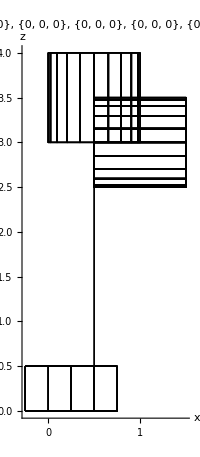

```mathematica
ShowRobot[{{q34,0,0},{q35,0,0},{q36,0,0},{q38,0,0},{q42,0,0},{q43,0,0},{q44,0,0},1},{animate->True}];
Show[robotplot]
```

## Save Jacobians

To save the associated Jacobians, comment out all testing code and run once each with the DOF in the DH file set to the relevant After values.

```mathematica
AfterShoulder
AfterElbow
AfterWrist
```

5

7

10

Also set the DOF & body segment name here, then run the following cell to save outputs

```mathematica
DOF=AfterShoulder;
SegName="UAR";
```

```mathematica
Export[NotebookDirectory[]<>"t_robotica/"<>SegName<>".txt",Simplify[T[0,DOF]]]
Export[NotebookDirectory[]<>"jacobians/"<>SegName<>".txt",Simplify[J]]
```

Export::nodir: Directory /Users/reembodied/Documents/workplace/SkeletonCapture/analysis/dynamics matrix construction/testing/t_robotica/ does not exist.

OpenWrite::noopen: Cannot open /Users/reembodied/Documents/workplace/SkeletonCapture/analysis/dynamics matrix construction/testing/t_robotica/UAR.txt.

$Failed

Export::nodir: Directory /Users/reembodied/Documents/workplace/SkeletonCapture/analysis/dynamics matrix construction/testing/jacobians/ does not exist.

OpenWrite::noopen: Cannot open /Users/reembodied/Documents/workplace/SkeletonCapture/analysis/dynamics matrix construction/testing/jacobians/UAR.txt.

$Failed